```mathematica
CExpressionToNumber[string_]:=ToExpression[StringReplace[string,{"e+":>"*^","e-":>"*^-"}]]
```

## Evolucion de uso

```mathematica
Languages={"EN","FR","GE","IT","SP"};ls={Language1="EN",Language2="FR"}
```

{EN,FR}

```mathematica
Colors=RGBColor@@@({{0,133,171},{255,117,0},{135,0,179},{48,130,5},{163,0,0}}/256);
```

```mathematica
s=Table[{Languages[[i]],Languages[[If[j≥i,j+1,j]]]},{i,Length[Languages]},{j,Length[Languages]-1}]
```

{{{EN,FR},{EN,GE},{EN,IT},{EN,SP}},{{FR,EN},{FR,GE},{FR,IT},{FR,SP}},{{GE,EN},{GE,FR},{GE,IT},{GE,SP}},{{IT,EN},{IT,FR},{IT,GE},{IT,SP}},{{SP,EN},{SP,FR},{SP,GE},{SP,IT}}}

```mathematica
GetData[{l1_,l2_}]:=CExpressionToNumber/@ReadList["Datos_art/Uso/Conjuntos/USO_a"<>l1<>"-"<>l2<>".txt",String];
GetData[{l1_Integer,l2_Integer},Languages_]:=GetData[{Languages[[l1]],Languages[[l2]]}]
```

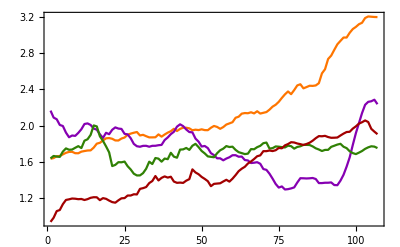
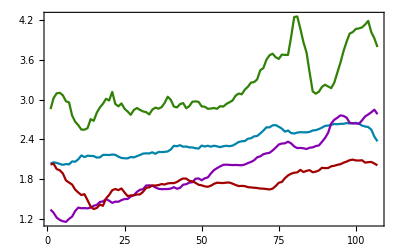
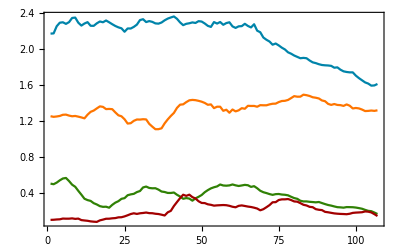
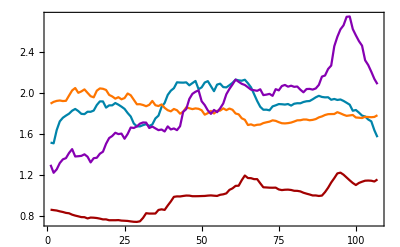
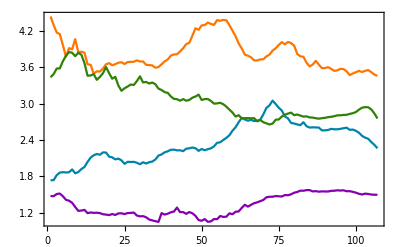

```mathematica
l1=1;
Table[
Show[Table[
pair={l1,l2};
data=10GetData[pair,Languages];
ListPlot[data,Joined->True,PlotStyle->Colors[[pair[[2]]]],PlotRange->All],{l2,Delete[Range[5],l1]}],PlotRange->All,Frame->True,Axes->False],{l1,5}]
```

## Pre figura de las columnas con el numero de palabras uqe migran

```mathematica
{n=5,y=11};
d=Table[
{d1=Table[RandomInteger[20],{y},{n-1}],
d2=Table[RandomInteger[80],{y}]},{n}];
```

```mathematica
claves={"EN","FR","GE","IT","SP"}
```

{EN,FR,GE,IT,SP}

```mathematica
d[[1]]
```

{{{7,5,6,8},{1,3,4,13},{13,5,8,5},{18,18,16,16},{10,2,9,9},{6,2,11,12},{12,20,5,19},{20,16,12,11},{20,14,0,19},{0,13,6,5},{16,11,20,20}},{59,11,57,51,59,63,51,22,4,75,47}}

```mathematica
ds={ReadList["!cut  DATOS/NW1_"<>#<>" -c 3-",Number,RecordLists->True],ReadList["!cut  DATOS/NW2_"<>#<>" -c 3-",Number,RecordLists->True]}&/@claves;
```

```mathematica
ticksx=Table[{i,10(i-1)+1900},{i,1,y,2}];
```

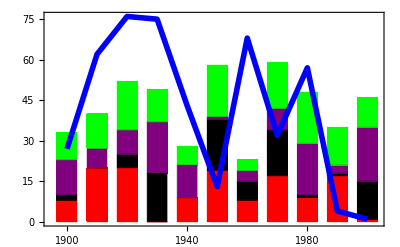

```mathematica
gDibujos[d_,l_,Colors_]:=Module[{gbc,gl},
gbc=BarChart[d[[l,1]],ChartLayout->"Stacked",ChartStyle->Delete[Colors,l],BarSpacing->.5,Axes->None];gl=ListPlot[d[[l,2]],Joined->True,PlotStyle->{Colors[[l]],Thickness[0.01]}];Show[{gbc,gl},Frame->True,FrameTicks->{ticksx,Automatic,None,None},PlotRange->All,PlotRangePadding->None]
]
Colors={Red,Blue,Black,Purple,Green};
gDibujos[d,l,Colors]
```

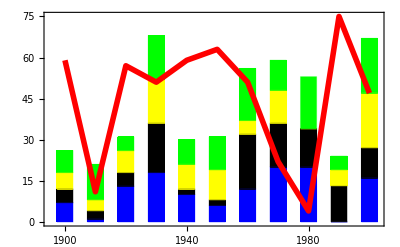
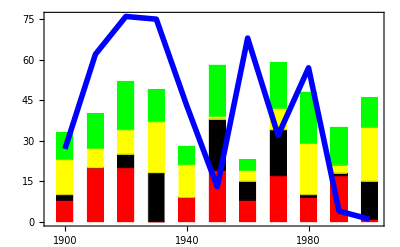
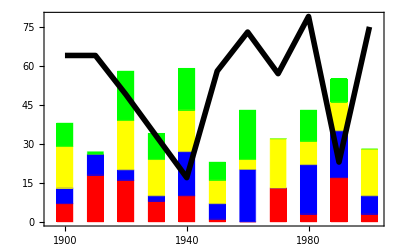
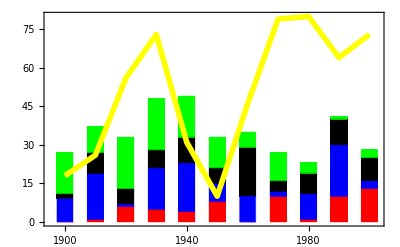
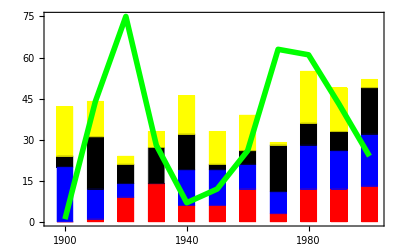

```mathematica
Table[gDibujos[d,l,Colors],{l,5}]
```